```mathematica
data = ReadList["./GitHub/PHYS-3181/homework1/spring_out.log",{Real,Real,Real}]
```

{{0.,0.,0.707107},{0.062832,0.125581,0.750111},{0.125664,0.250666,0.790155},{0.188496,0.374763,0.827081},{0.251327,0.49738,0.860742},{0.314159,0.618034,0.891007},{0.376991,0.736249,0.917755},{0.439823,0.851559,0.940881},{0.502655,0.963507,0.960294},{0.565487,1.07165,0.975917},{0.628319,1.17557,0.987688},{0.69115,1.27485,0.995562},{0.753982,1.36909,0.999507},{0.816814,1.45794,0.999507},{0.879646,1.54103,0.995562},{0.942478,1.61803,0.987688},{1.00531,1.68866,0.975917},{1.06814,1.75261,0.960294},{1.13097,1.80965,0.940881},{1.19381,1.85955,0.917755},{1.25664,1.90211,0.891007},{1.31947,1.93717,0.860742},{1.3823,1.96458,0.827081},{1.44513,1.98423,0.790155},{1.50796,1.99605,0.750111},{1.5708,2.,0.707107},{1.63363,1.99605,0.661312},{1.69646,1.98423,0.612907},{1.75929,1.96458,0.562083},{1.82212,1.93717,0.509041},{1.88496,1.90211,0.45399},{1.94779,1.85955,0.397148},{2.01062,1.80965,0.338738},{2.07345,1.75261,0.278991},{2.13628,1.68866,0.218143},{2.19912,1.61803,0.156434},{2.26195,1.54103,0.094108},{2.32478,1.45794,0.031411},{2.38761,1.36909,-0.031411},{2.45044,1.27485,-0.094108},{2.51327,1.17557,-0.156434},{2.57611,1.07165,-0.218143},{2.63894,0.963507,-0.278991},{2.70177,0.851559,-0.338738},{2.7646,0.736249,-0.397148},{2.82743,0.618034,-0.45399},{2.89027,0.49738,-0.509041},{2.9531,0.374763,-0.562083},{3.01593,0.250666,-0.612907},{3.07876,0.125581,-0.661312},{3.14159,0.,-0.707107},{3.20443,-0.125581,-0.750111},{3.26726,-0.250666,-0.790155},{3.33009,-0.374763,-0.827081},{3.39292,-0.49738,-0.860742},{3.45575,-0.618034,-0.891007},{3.51858,-0.736249,-0.917755},{3.58142,-0.851559,-0.940881},{3.64425,-0.963507,-0.960294},{3.70708,-1.07165,-0.975917},{3.76991,-1.17557,-0.987688},{3.83274,-1.27485,-0.995562},{3.89558,-1.36909,-0.999507},{3.95841,-1.45794,-0.999507},{4.02124,-1.54103,-0.995562},{4.08407,-1.61803,-0.987688},{4.1469,-1.68866,-0.975917},{4.20973,-1.75261,-0.960294},{4.27257,-1.80965,-0.940881},{4.3354,-1.85955,-0.917755},{4.39823,-1.90211,-0.891007},{4.46106,-1.93717,-0.860742},{4.52389,-1.96458,-0.827081},{4.58673,-1.98423,-0.790155},{4.64956,-1.99605,-0.750111},{4.71239,-2.,-0.707107},{4.77522,-1.99605,-0.661312},{4.83805,-1.98423,-0.612907},{4.90089,-1.96458,-0.562083},{4.96372,-1.93717,-0.509041},{5.02655,-1.90211,-0.45399},{5.08938,-1.85955,-0.397148},{5.15221,-1.80965,-0.338738},{5.21504,-1.75261,-0.278991},{5.27788,-1.68866,-0.218143},{5.34071,-1.61803,-0.156434},{5.40354,-1.54103,-0.094108},{5.46637,-1.45794,-0.031411},{5.5292,-1.36909,0.031411},{5.59204,-1.27485,0.094108},{5.65487,-1.17557,0.156434},{5.7177,-1.07165,0.218143},{5.78053,-0.963507,0.278991},{5.84336,-0.851559,0.338738},{5.90619,-0.736249,0.397148},{5.96903,-0.618034,0.45399},{6.03186,-0.49738,0.509041},{6.09469,-0.374763,0.562083},{6.15752,-0.250666,0.612907},{6.22035,-0.125581,0.661312},{6.28319,0.,0.707107}}

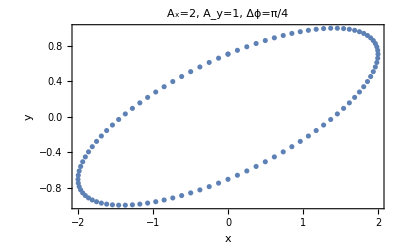

```mathematica
g = ListPlot[Transpose[{data[[All,2]],data[[All,3]]}],Frame->True,FrameLabel->{"x","y"},PlotLabel->"A_x=2, A_y=1, Δϕ=π/4"]
```

```mathematica
Export["C:\\Users\\Caden Gobat\\Documents\\GitHub\\PHYS-3181\\homework1\\plot.pdf",g]
```

C:\Users\Caden Gobat\Documents\GitHub\PHYS-3181\homework1\plot.pdf